## Expanding spheroidal harmonics into spherical harmonics

Scott A. Hughes, 28 May 2018

As originally shown in Appendix A of PRD 61, 084004 (2000), spheroidal harmonics can be written quite nicely as an expansion in spherical harmonics; finding the expansion coefficients amounts to then finding the eigenvectors of a particular matrix (for which the eigenvalue is the corresponding eigenvalue of the spheroidal harmonic).  I have C/C++ code that does this for real mode frequencies.   Generalizing this code to complex frequencies proves to be somewhat tricky, since the C code uses techniques which assume that the matrix elements are all real.  Fortunately, Mathematica provides good tools for finding the eigenvalues and eigenvectors of complex matrices.

Note that the technique coded up here appears to be identical to that described in Cook and Zalutskiy, PRD 90, 124021 (2014) [also arXiv:1410.7698] for the angular eigenfunction.

```mathematica
ClearAll["Global`*"]
```

### Fundamentals

Entries of this matrix involve integrals of  cos(theta) or cos(theta)^2 against two spin-weighted spherical harmonics; see Hughes 2000 for details.  The result can be expressed as a product of ClebschGordan coefficients.  Note that spin-weight -2 is assumed here:

```mathematica
cossqbrac[l_,j_,m_] = (1/3)KroneckerDelta[j,l]+(2/3)Sqrt[(2j+1)/(2l+1)]ClebschGordan[{j,m},{2,0},{l,m}]ClebschGordan[{j,2},{2,0},{l,2}];
cosbrac[l_,j_,m_]=Sqrt[(2j+1)/(2l+1)]ClebschGordan[{j,m},{1,0},{l,m}]ClebschGordan[{j,2},{1,0},{l,2}];
```

Here is the matrix; spin-weight -2 assumed.

```mathematica
Mij[aw_, p_,q_,m_] = -If[p==q,(aw)^2cossqbrac[p,q,m]+4aw cosbrac[p,q,m]-p(p+1),If[p==q-1||p==q+1,(aw)^2cossqbrac[p,q,m]+4 aw cosbrac[p,q,m],If[p==q-2||p==q+2,(aw)^2cossqbrac[p,q,m],0]]];
```

The indices of the matrix begin at lmin, which is the maximum of 2 (absolute value of spin weight) or |m|, and continue to some value lmax.  Strictly speaking, lmax should be infinite, but for numerical purposes is truncated at some finite value (more on this below).

```mathematica
lmin[m_] = Max[2,Abs[m]];
```

```mathematica
SWSHMatrix[aw_,m_,lmax_] := Table[Table[Mij[aw,p,q,m],{p,lmin[m],lmax}],{q,lmin[m],lmax}]
SWSHExpansion[aw_,m_,lmax_] := Eigensystem[SWSHMatrix[aw,m,lmax]]
```

The eigensystem now contains our complete solution for the eigenvalue and the expansions coefficients.  Entry 1 of the table contains the (lmax - lmin + 1) eigenvalues, ordered from largest to smallest.  Entry 2 is a matrix, each row of which is an eigenvector of expansion coefficients, ordered in the same way as the eigenvalues.

Note the offset by 2 on the eigenvalue.  This is because the matrix above produces the eigenvalue E_{lm} = l(l+1) in the Schwarzschild limit.  To compare with Berti, we want A_{lm} = E_{lm}-s(s+1) = E_{lm}-2.

Note that the code keeps everything symbolic for as long as possible.  I use “InputForm” and “N[]” in order to have Mathematica report its results to machine precision.

```mathematica
SWSHEigenvalue[l_,m_,aw_,lmax_] := InputForm[N[SWSHExpansion[aw,m,lmax][[1,lmax-l+1]]-2]]
SWSHSphericalCofs[l_,m_,aw_,lmax_]:= InputForm[N[SWSHExpansion[aw,m,lmax][[2,lmax-l+1]]]]
```

### Real frequency example

Here are some examples for real frequencies, for which we can compare against the C code.  Some experimentation may be needed to figure out a good choice for lmax.  The rule of thumb is that it should be several integers beyond the l value whose expansion you want.  Try a few and assess when you find numerical convergence.

```mathematica
ToExpression[ToString[SWSHEigenvalue[5,2,0.99,7]]]
```

27.118

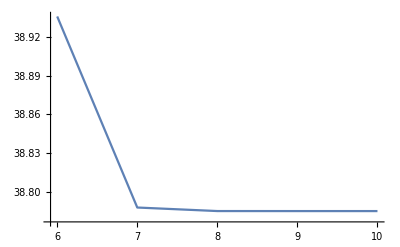

```mathematica
ListPlot[Table[{lindex,ToExpression[ToString[SWSHEigenvalue[6,5,0.99,lindex]]]},{lindex,5,10}],PlotRange->All,Joined->True]
```

If you want to pick out individual coefficients, the most computationally effective way to do this is to define an object which holds them, then scan through that object:

```mathematica
coeffshere = SWSHSphericalCofs[5,3,0.4,25]
```

{-0.000726750814007203, 0.06091987187262058, -0.9965706525527702, 
-0.05593169894177613, -0.002610176561415769, -0.00008683489423676252, 
-2.5151551749623356*^-6, -6.107817087756685*^-8, -1.329564913862617*^-9, 
-2.563431455275872*^-11, -4.517050965699247*^-13, -7.246238654938947*^-15, 
-1.076979984275681*^-16, -1.3456261469458784*^-18, 1.7960449287855412*^-18, 
-1.206857772945391*^-19, 3.7039523228522486*^-21, -1.1980259975628946*^-22, 
1.6001120332934363*^-24, -4.970416985246059*^-26, 2.5510857162502528*^-28, 
-1.258989199953356*^-29, 0.}

If you want to pull out a value corresponding to a particular k, you need to offset things a bit.  For example, the coefficient for the k = 5 spherical harmonic contribution to the l = 5 spheroidal harmonic is

```mathematica
k = 5;
InputForm[coeffshere[[1,k - lmin[3]+1]]]
```

-0.9965706525527702

Eigenvalues and expansion coefficients agree to all digits shown for every case I’ve examined for real frequencies.   Note that Eigensystem[] sometimes returns eigenvectors with the sign reversed from what we would like.  For real frequencies, if the entry whose value is closest to 1 is negative, then all coefficients should be multiplied by -1.

### Complex frequency example

Let’s try some complex frequencies now.  From Berti’s tables, for  l = 5, m = 3:

```mathematica
a = 0.9;
ωR = 1.425862206;
ωI = -0.07166423277;
awhere = a*(ωR + I ωI);
```

```mathematica
SWSHEigenvalue[3,3,awhere,30]
```

6.501129074039833 + 0.22876409025102423*I

This agrees with the eigenvalue shown in Berti’s tables (as well as using the QNM notebook he provides on his website).

```mathematica
coeffshere = SWSHSphericalCofs[3,3,awhere,30]
```

{0.9791903052245325 + 0.*I, 0.20020262686692325 - 0.010739796199136573*I, 
0.031056786063379162 - 0.003220066399412456*I, 
0.0038091287605118117 - 0.0005891789371566418*I, 
0.00039233319283452675 - 0.00008082546980399168*I, 
0.00003463088492016716 - 8.955822465049902*^-6*I, 
2.682650403990744*^-6 - 8.382952809411315*^-7*I, 
1.8466060519395849*^-7 - 6.798943127261746*^-8*I, 
1.1445285556702057*^-8 - 4.875189609181079*^-9*I, 
6.441231650743414*^-10 - 3.132452535730745*^-10*I, 
3.3195664169665416*^-11 - 1.824711789339651*^-11*I, 
1.576009953611784*^-12 - 9.719128838748512*^-13*I, 
6.933495478905429*^-14 - 4.77011371097822*^-14*I, 
2.8390283804422798*^-15 - 2.1701494789531702*^-15*I, 
1.0865585718962274*^-16 - 9.20222988727562*^-17*I, 
3.899638312692759*^-18 - 3.653104320365745*^-18*I, 
1.3165233817505515*^-19 - 1.363278793255334*^-19*I, 
4.190902684892227*^-21 - 4.798967673675303*^-21*I, 
1.260703900640674*^-22 - 1.5986153572343844*^-22*I, 
3.589602678174469*^-24 - 5.053099620497574*^-24*I, 
9.686982544408704*^-26 - 1.519513426826992*^-25*I, 
2.479521345065106*^-27 - 4.3566206892804984*^-27*I, 
6.021707819324425*^-29 - 1.1934544949486318*^-28*I, 
1.3868791333956333*^-30 - 3.129494916382086*^-30*I, 
3.025065697128922*^-32 - 7.868902266163266*^-32*I, 
6.2311235969642455*^-34 - 1.900202693968849*^-33*I, 
1.205873594316196*^-35 - 4.413384087843086*^-35*I, 
2.1719385804528963*^-37 - 9.871364625156645*^-37*I}

Same deal with needing to make an offset if you want a particular coefficient:

```mathematica
k = 5;
coeffshere[[1,k-lmin[3]+1]]
```

0.0310568-0.00322007 ⅈ

Interesting note: I’m finding that the k = l coefficients agree very well in magnitude with the values in Berti’s tables for all the cases I have examined.  The phase differs, however: “EigenSystem” chooses to make the corresponding component of the eigenvector be purely real.  This is consistent with the choice that Cook and Zalutskiy make (ie, that their coefficient $C_{l’lm}$ be purely real if $l = l’$).

Somewhat disturbingly, I’m find that the coefficients for k != l do not agree in magnitude with Berti’s tables.  They’re not badly off, but they definitely differ.  I have not been able to find an error, however.  I plan to ask Greg Cook if he can provide some comparison coefficients, just to double check whether we have something wrong.  It is odd that we agree so well for real frequencies, so well for k == l (modulo phase, which is somewhat arbitrary), but disagree for this remaining case.  It is possible we are not quite computing the same thing; but if that’s the case, I’d like to understand what’s going on better.

### Addendum Comparison

#### Some Modules To Load Berti’s Tables

```mathematica
QNMDIR="/Volumes/halston_lim/Research_Documents/2019_Hughes_Khanna_Apte_QNM/kerr_table/";
SWSHDIR="/Volumes/halston_lim/Research_Documents/2019_Hughes_Khanna_Apte_QNM/swsh_table/";
```

```mathematica
σQNM[mmode_,ℓ_,m_,n_,af_]:=Module[{res,tmp,ωQNM,InverseτQNM,sign},
If[af≥0,
(*POSITIVE SPINS HERE*)
If[m≥0,If[FileExistsQ[QNMDIR<>"n"<>ToString[n+1]<>"l"<>ToString[ℓ]<>"m"<>ToString[m]<>".dat"],tmp=Import[QNMDIR<>"n"<>ToString[n+1]<>"l"<>ToString[ℓ]<>"m"<>ToString[m]<>".dat"];
ωQNM=Interpolation[{#[[1]],#[[2]]}&/@tmp];
InverseτQNM=Interpolation[{#[[1]],#[[3]]}&/@tmp];
res=ωQNM[af]+I InverseτQNM[af];
,
res=0];
,
res=σQNM[mmode,ℓ,-m,n,-af]];
,
(*NEGATIVE SPINS HERE*)
If[m≥0,If[FileExistsQ[QNMDIR<>"n"<>ToString[n+1]<>"l"<>ToString[ℓ]<>"mm"<>ToString[m]<>".dat"],
tmp=Import[QNMDIR<>"n"<>ToString[n+1]<>"l"<>ToString[ℓ]<>"mm"<>ToString[m]<>".dat"];
ωQNM=Interpolation[{-#[[1]],#[[2]]}&/@tmp];
InverseτQNM=Interpolation[{-#[[1]],#[[3]]}&/@tmp];
res=ωQNM[af]+I InverseτQNM[af];
,
res=0;Print["help"]];
,
res=σQNM[mmode,ℓ,-m,n,-af]];
];
res];
```

```mathematica
mulmlpnp[l_,lp_,m_,npr_,a_]:=Module[{realmu,imagmu,filepath,tmp,res},
filepath=SWSHDIR<>"l"<>ToString[l]<>If[ m≥0,"m"<>ToString[m],"mm"<>ToString[Abs[m]]]<>"lp"<>ToString[Abs[lp]]<>"np"<>ToString[npr]<>".dat";
tmp=Import[filepath];
realmu=Interpolation[{#[[1]],#[[2]]}&/@tmp];
imagmu=Interpolation[{#[[1]],#[[3]]}&/@tmp];
res=(realmu[a]+I*imagmu[a]);
res
];
```

#### Comparison

```mathematica
(* Spheroidal Harmonic index (l,m) Spherical Harmonic index (k) *)
{k,l,m,spin} = {6,6,5,.9};
n=0;
ω=σQNM[m,l,m,n,spin];
awval=spin*ω;
(* Hughes *)
(* Defined in Hughes 2000 *)
SWSHSphericalCofs[l,m,awval,30];
coeffshere = SWSHSphericalCofs[l,m,awval,30][[1,k-lmin[m]+1]]
(* Berti *)
(* Defined in Berti 2014 as complex conjugate of Hughes 2000 def*)
Conjugate[mulmlpnp[k,l,m,n,spin]];
```

0.964302+0. ⅈ

```mathematica
OUTDIR="/Volumes/halston_lim/Research_Documents/2019_Hughes_Khanna_Apte_QNM/swsh_table_hughes/new/";
```

```mathematica
table=Table[{spin,Re[SWSHSphericalCofs[l,m,spin*σQNM[m,l,m,n,spin],30][[1,k-lmin[m]+1]]]//N,-Im[SWSHSphericalCofs[l,m,spin*σQNM[m,l,m,n,spin],30][[1,k-lmin[m]+1]]//N]},{spin,.99,.99,.1}]
```

{{0.99,0.932794,0.}}

```mathematica
WriteSWSHTable[k_,l_,m_,n_]:=Module[{filename,table,omegaqnm},
filename="l"<>ToString[k]<>"m"<>If[m≥0,ToString[m],"m"<>ToString[Abs[m]]]<>"lp"<>ToString[l]<>"np"<>ToString[n]<>".dat";
table=Table[{spin,Re[SWSHSphericalCofs[l,m,spin*σQNM[m,l,m,n,spin],30][[1,k-lmin[m]+1]]],-Im[SWSHSphericalCofs[l,m,spin*σQNM[m,l,m,n,spin],30][[1,k-lmin[m]+1]]]},{spin,{0}}];Export[OUTDIR<>filename,table,"Table"]
];
```

```mathematica
Clear[spin];
modecases={};
n=0;
For[l=2,l≤8,l++,
For[k=2,k≤8,k++,
For[m=-Min[l,k],m≤Min[l,k],m++,
modecases=Append[modecases,{k,l,m}]]]];
```

```mathematica
For[i=1,i≤Length[modecases],i++,
WriteSWSHTable[modecases[[i]][[1]],modecases[[i]][[2]],modecases[[i]][[3]],n]]
```